```mathematica
ClearAll["Global`*"]
```

```mathematica
K[n_] := If[n==1,0,FullSimplify[ MangoldtLambda[n]/Log[n]]]
pref9[n_,k_,a_,c_]:=pref9[n,k,a,c]=
Sum[K[Floor[a j]]pref9[Floor[n/j],k-1,a,c],{j,2,n}]-c Sum[K[Floor[a j c]]pref9[Floor[n/(j c)],k-1,a,c],{j,1,n/c}];pref9[n_,0,a_,c_]:=1
pref8[n_,k_,a_,c_]:=pref8[n,k,a,c]=
Sum[K[Floor[a j]]pref8[Floor[n/j],k-1,a,c],{j,1,n}]-c Sum[K[Floor[a j c]]pref8[Floor[n/(j c)],k-1,a,c],{j,1,n/c}];pref8[n_,0,a_,c_]:=1
pref8a[n_,s_]:=Sum[ s^k pref8[n/(s^k),1,s^k,s],{k,0,Log[s,n]}]
pref8b[n_,k_,b_]:=Sum[Binomial[k+j-1,k-1] b^j pref8[n/b^j, k, b^j,b],{j,0,Log[b,n]}]
```

```mathematica
pref[n_,k_] := pref[n,k]=Sum[ (-1)^(j+1)K[j]pref[Floor[n/j],k-1],{j,2,n}];pref[n_,0]:=1
prefa[n_,k_] := Sum[ (-1)^(j+1)K[j]prefa[Floor[n/j],k-1],{j,1,n}];prefa[n_,0]:=1
tt[n_,k_]:=Mod[n,k]-Mod[n-1,k]

pref2[n_,k_,a_]:=pref2[n,k,a]=Sum[ tt[j,a]K[j]pref2[Floor[n/j],k-1,a],{j,2,n}];pref2[n_,0,a_]:=1
pref2a[n_,k_,a_]:=Sum[ tt[j,a]K[j]pref2a[Floor[n/j],k-1,a],{j,1,n}];pref2a[n_,0,a_]:=1

ptest[n_, z_] := Sum[ z^k/(k!) pref[n,k],{k,1,Log[2,n]}]
ptest2[n_, z_,a_] := Sum[ z^k/(k!) pref2[n,k,a],{k,1,Log[2,n]}]
ptest3[n_, z_,a_] := Sum[ z^k/(k!) pref9[n,k,1,a],{k,1,Log[a,n]}]
```

```mathematica
pref8a[100,2]
```

428/15

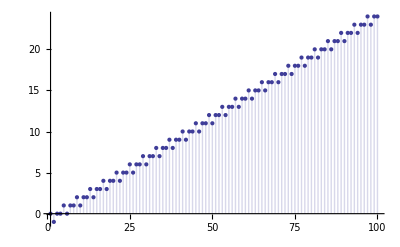

```mathematica
DiscretePlot[ptest[n,1],{n,1,100}]
```

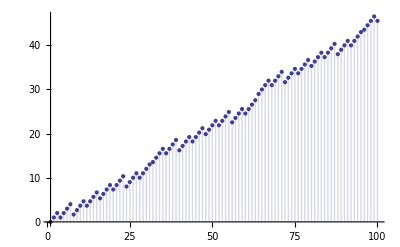

```mathematica
DiscretePlot[ptest2[n,1,4],{n,1,100}]
```

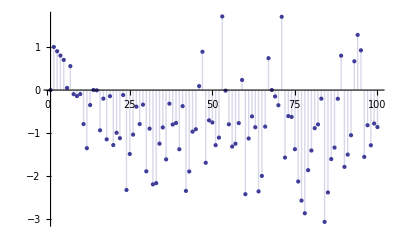

```mathematica
DiscretePlot[ptest3[n,1,1.1],{n,1,100}]
```

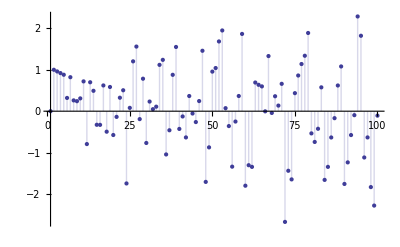

```mathematica
DiscretePlot[ptest3[n,1,1.04],{n,1,100}]
```

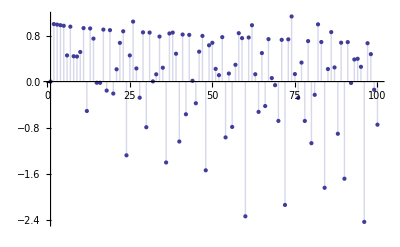

```mathematica
DiscretePlot[ptest3[n,1,1.01],{n,1,100}]
```

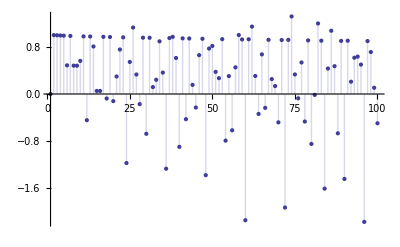

```mathematica
DiscretePlot[ptest3[n,1,1.003],{n,1,100}]
```

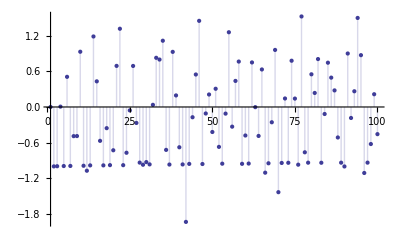

```mathematica
DiscretePlot[ptest3[n,-1,1.003],{n,1,100}]
```